# Coordenadas Baricéntricas

A continuación incluimos instrucciones de Mathematica para trabajar con coordenadas baricéntricas.

Multitud de ideas sugeridas por mi amigo Ercole Suppa. 
Francisco Javier García Capitán, 2006-2011.

25-Oct-2011. Modificado RazonSimple (añadido un Simplify para evitar Indeterminate en un caso especial)
30-Ago-2011. Añadida definición general de triángulo anticeviano.
08-Oct-2010. Modificado ConicaEnvolventeRectas para evitar fallos cuando faltan los coeficientes de t^2.
20-Sep-2010. Modificado SonParalelas para que funcione SonParalelas[r,r]->True
19-Sep-2010. SonHomoteticos
14-Sep-2010. Transformar. EvaluarExpresion.
13-Sep-2010. BisectrizInterior, EsInterior e Incentro.
8-Sep-2010. Modificación de TriánguloRectas. Añadido ptN=centro de los  puntos.

```mathematica
$Assumptions={a>0,b>0,c>0,a+b-c>0,a+c-b>0,b+c-a>0};
```

## Números

### El semiperímetro

```mathematica
s::"usage" = "La constante s representa el semiperímetro del triángulo de referencia";
```

```mathematica
s=(a+b+c)/2;
```

### Notación de Conway

```mathematica
SA::"usage" = "SA, SB, SC son las cantidades usadas en la notación de Conway.";
SB::"usage" = "SA, SB, SC son las cantidades usadas en la notación de Conway.";
SC::"usage" = "SA, SB, SC son las cantidades usadas en la notación de Conway.";
```

```mathematica
SA=(b^2+c^2-a^2)/2;SB=(c^2+a^2-b^2)/2;SC=(a^2+b^2-c^2)/2;
```

## Puntos y rectas concretos

### Los vértices y los lados del triángulo

Los vértices y lados del triángulo de referencia ABC tienen las expresiones más simples. Podemos hacer asignaciones múltiples, teniendo en cuenta que  Mathematica devuelve el valor de una asignación:

```mathematica
rtBC = ptA = {1, 0, 0};
rtCA = ptB = {0, 1, 0};
rtAB = ptC = {0, 0, 1};
```

### Baricentro, circuncentro y ortocentro

```mathematica
ptG={1,1,1};
ptO=Simplificar[{a^2 SA, b^2 SB, c^2 SC}];
ptH=Simplificar[{SB SC, SC SA, SA SB}];
ptN=Medio[ptH,ptO];
```

### El incentro y el punto simediano

```mathematica
ptI={a,b,c};ptK={a^2,b^2,c^2};
```

### Los tres excentros

```mathematica
ptIa = {-a, b, c};
ptIb = {a, -b, c};
ptIc = {a, b, -c};
```

### Puntos de contacto con los lados de la circunferencia inscrita

```mathematica
ptIX = {0, s - c, s - b};
ptIY = {s - c, 0, s - a};
ptIZ = {s - b, s - a, 0};
```

### Puntos de contacto de los lados con las circunferencias exinscritas

```mathematica
ptIaX = {0, s-b, s-c}; ptIaY={s-b,0,-s};    ptIaZ = {s-c,-s,0};
ptIbX = {0, s-a, -s};    ptIbY = {s - a, 0, s - c}; ptIbZ = {-s, s - c, 0};
ptIcX = {0, -s, s - a};    ptIcY = {-s, 0, s - b};    ptIcZ = {s - a, s - b, 0};
```

## Operaciones abstractas

### Comprobar si un punto es del infinito

Un punto es infinito si y solo si sus coordenadas baricéntricas suman cero.

```mathematica
EsInfinito::"usage" = "EsInfinito[ptP] devuelve True si ptP es un punto infinito.";
```

```mathematica
EsInfinito[ptX_]:=SameQ[Factor[Total[ptX]],0];
```

Ejemplo:

```mathematica
ptP={2a-b-c,b-a,c-a};
EsInfinito[ptP]
```

True

### Permutación de coordenadas

```mathematica
ReglaDePermutacion::"usage" = "ReglaPermutacion es una constante que indica los símbolos que se usarán al permutar una expresón. Por defecto su valor es Thread[{a,b,c,α,β,γ,u,v,w,x,y,z}→{b,c,a,β,γ,α,v,w,u,y,z,x}]";
```

```mathematica
ReglaDePermutacion=Thread[{a,b,c,α,β,γ,u,v,w,p,q,r,x,y,z}-> {b,c,a,β,γ,α,v,w,u,q,r,p,y,z,x}];
```

Esta función será util cuando hemos efectuado un cálculo que toma como base un lado o ángulo del triángulo de referencia ABC y queremos efectuar el cálculo correspondiente a los otros lados o ángulos:

```mathematica
Permutar::"usage"="Permutar[f] tranforma la expresión f teniendo en cuenta la constante ReglaDePermutacion.";
```

```mathematica
Permutar[f_]:= f /.ReglaDePermutacion;
```

```mathematica
PermutarTerna::"usage"="PermutarTerna[{p,q,r}}] tranforma la terna {p,q,r} en la terna {r,p,q}, efectuando a la vez las transformaciones definidas por ReglaDePermutacion";
```

```mathematica
PermutarTerna[{x1_,x2_,x3_}]:={x3,x1,x2} /.ReglaDePermutacion;
```

```mathematica
TernaCiclica::"usage" = "TernaCiclica[f] tranforma la expresión f en {f,g,h} siendo g=Permutar[f] y h=Permutar[g]";
```

```mathematica
TernaCiclica[f_] := Table[Nest[Permutar, f, n],{n,0,2}]
```

```mathematica
SumaCiclica::"usage" = "SumaCiclica[f] halla la suma de los elementos de su terna cíclica {f,g,h}";
```

```mathematica
SumaCiclica[f_]:= Total[TernaCiclica[f]]
```

```mathematica
EsCiclica::"usage" = "EsCiclica[expr] devuelve True si expr es cíclica";
```

```mathematica
EsCiclica[expr_]:=TernaCiclica[expr]==={expr,expr,expr};
```

```mathematica
GeneradorCiclico::"usage" = "GeneradorCiclico[expr] devuelve el generador cíclico de una expresión cíclica";
```

```mathematica
GeneradorCiclico[expr_]:=Module[{ lista1,lista2},
lista1=Apply[List, Expand[expr]];
lista2={};
While[lista1 ≠  {},
lista2=Append[lista2,First[lista1]];
lista1=Complement[lista1,TernaCiclica[First[lista1]]]
];
Apply[Head[expr], lista2]
];
```

```mathematica
GeneradorCiclico[a b c]
```

a

```mathematica
GeneradorCiclico2[expr_]:=Module[{expr1,t,gen},
If[EsCiclica[expr],
gen=0;expr1=expr;
While[expr1=!=0,
t=If[Head[expr1]===Plus,First[expr1],expr1];
gen=gen+If[EsCiclica[t],Divide[t,3],t];
expr1=expr1-If[EsCiclica[t],t,SumaCiclica[t]]
];
gen,Print["Uncyclic expression"]]
]
```

```mathematica
GeneradorCiclico2[a b c]
```

(a b c)/3

### Sustituir un punto

```mathematica
Sustituir::"usage" = "Sustituir[expr,variable,valor] sustituye en la expresión expr el punto variable por el punto valor. Así Sustituir[expr,{x,y,z}, ptO] sustituirá {x,y,z} por las coordenadas del circuncentro";
```

```mathematica
Sustituir[expr_,variable_,valor_]:=Factor[expr /. Thread[variable->valor]];
```

Se supone que f es una expresión en u, v, w y queremos sustituir (u, v, w) por (x, y, z):

```mathematica
Sustituiruvw::"usage" = "Sustituiruvw[f, {x,y,z}] sustituye {u,v,w} por {x,y,z}";
```

```mathematica
Sustituiruvw[f_,{α_,β_,γ_}]:=Sustituir[f,{u,v,w},{α,β,γ}] ;
```

Se supone que f es una expresión en x, y, z y queremos sustituir (x, y, z) por (u, v,w):

```mathematica
Sustituirxyz::"usage" = "Sustituirxyz[f, {u,v,w}] sustituye {x,y,z} por {u,v,w}";
```

```mathematica
Sustituirxyz[f_,{α_,β_,γ_}]:=Sustituir[f,{x,y,z},{α,β,γ}] ;
```

### Regla para sustituir potencias del área

```mathematica
fS2::"usage" = "fS2 representa la fórmula del cuadrado del doble del área del triángulo ABC";
```

```mathematica
sustS::"usage" = "sustS reduce expresiones en las que aparezcan potencias de S (doble del área del triángulo ABC) y devuelve una exprexión en la que sólo aparece S";
```

```mathematica
fS2=Expand[4s(s-a)(s-b)(s-c)];
sustS={S^n_->fS2^Quotient[n,2] S^Mod[n,2]};
```

### Reglas para sustituir a, b, c por SA, SB, SC.

```mathematica
sustSASBSC::"usage" = "sustS reduce expresiones en las que aparezcan potencias de S (doble del área del triángulo ABC) y devuelve una exprexión en la que sólo aparece S";
```

```mathematica
sustSASBSC={a^n_->(sb+sc)^Quotient[n,2] a^Mod[n,2],b^n_->(sc+sa)^Quotient[n,2] b^Mod[n,2],c^n_->(sa+sb)^Quotient[n,2] c^Mod[n,2]};
```

### Simplificación de coordenadas

Las coordenadas baricéntricas homogéneas de un punto y los coeficientes de la ecuación de una recta los introducimos en Mathematica como ternas de puntos. Como dos de estas ternas se consideran equivalentes cuando son proporcionales, usamos la función Simplificar para conseguir la expresión más sencilla:

```mathematica
Simplificar::"usage" = "Simplificar devuelve una terna dividida por su Máximo Común Divisor";
```

```mathematica
Simplificar[lista_]:=Simplify[lista/Apply[PolynomialGCD,lista]]
```

### Simetrización de coordenadas

```mathematica
Simetrizar::"usage" = "Simetrizar convierte en simétricas coordenadas de un punto que no lo son. Normalmente, por la presentcia de alguna raíz cuadrada";
```

```mathematica
Simetrizar[ptP_]:=Simplificar[Total[Table[Nest[PermutarTerna, ptP,n],{n,0,2}]]]
```

## Cálculo de puntos y rectas

### Coordenadas de un punto y ecuación de una recta

Aprovechando la dualidad entre coordenadas de puntos y ecuaciones de rectas, podemos usar para ambos la función Cross para hallar el punto de intersección de dos rectas y la recta que une dos puntos.

```mathematica
Recta::"usage"="Recta[P,Q] halla los coeficientes de la ecuación de la recta PQ";
```

```mathematica
Recta[P_,Q_] :=Simplificar[Cross[P,Q]];
```

```mathematica
Punto::"usage"="Punto[r,s] halla las coordenadas de la intersección de las rectas r y s";
```

```mathematica
Punto[r_,s_] := Simplificar[Cross[r,s]];
```

### Punto del infinito de una recta

El punto del infinito de la recta p x +q y + r z=0 tiene coordenadas (q-r: r-p : p-q)

```mathematica
PuntoInfinito::"usage" = "PuntoInfinito[{p,q,r}] devuelve el punto del infinito de la recta px + qy + rz=0";
```

```mathematica
PuntoInfinito[{p_,q_,r_}] := {q-r,r-p,p-q};
```

### Recta paralela a otra que pasa por un punto

```mathematica
Paralela::"usage" = "Paralela[P,r] devuelve la recta paralela a r que pasa por el punto P. \nParalela[P, Q, R] devuelve la recta paralela a la recta QR que pasa por el punto P.";
```

Calculamos la recta paralela a una recta r pasando por un punto P:

```mathematica
Paralela[P_, r_] := Recta[P,PuntoInfinito[r]];
```

Calculamos la recta paralela a una recta QR pasando por un punto P:

```mathematica
Paralela[P_, Q_,R_] := Paralela[P, Recta[Q,R]];
```

### Punto del infinito de rectas perpendiculares

Si una recta tiene a (f:g:h) como punto del infinito, entonces el punto del infinito de cualquier recta perpendicular a ella es el punto del infinito de la recta (SA f )x + (SB g) y + (SC h) z =0.

```mathematica
PuntoInfinitoPerpendicular::"usage"="Perpendicular[{f,g,h}] devuelve el punto del infinito de la recta cuyo punto del infinito es {f,g,h}";
```

```mathematica
PuntoInfinitoPerpendicular[{f_,g_,h_}] :=
PuntoInfinito[{SA f, SB g, SC h}];
```

### Recta perpendicular a otra pasando por un punto

```mathematica
Perpendicular::"usage" = "Perpendicular[P,r] devuelve la recta perpendicular a r que pasa por el punto P. \nPerpendicular[P, Q, R] devuelve la recta perpendicular a la recta QR que pasa por el punto P.";
```

```mathematica
Perpendicular[P_,r_] :=Recta[P,PuntoInfinitoPerpendicular[PuntoInfinito[r]]];
```

```mathematica
Perpendicular[P_,Q_,R_]:=Perpendicular[P,Recta[Q,R]];
```

### Comprobación de paralelismo y perpendicularidad

```mathematica
SonParalelas::"usage" = "SonParalelas[r,s] devuelve True si las rectas r y s son paralelas";
```

```mathematica
SonParalelas[r_, s_] := Factor[PuntoInfinito[r].s] == 0;
```

```mathematica
SonPerpendiculares::"usage" = "SonPerpendiculares[r,s] devuelve True si las rectas r y s son perpendiculares";
```

```mathematica
SonPerpendiculares[r_,s_]:=Simplify[PuntoInfinitoPerpendicular[PuntoInfinito[r]].s]==0;
```

### Cuarta recta

Dadas tres rectas r1, r2, r3 hallamos la recta r4 que forma con la recta r3 el mismo ángulo que la recta r1 forma con la recta r2. Esta implementación se basa en un análisis hecho por Paul Yiu.

```mathematica
PuntoInfinitoCuartaRecta::"usage" = "PuntoInfinitoCuartaRecta[r1,r2,r3] devuelve el punto del infinito de la recta r4 que forma con la recta r3 el mismo ángulo que la recta r1 forma con la recta r2";
```

```mathematica
PuntoInfinitoCuartaRecta[r1_,r2_,r3_] := Module[
{S2,u1,v1,w1,u2,v2,w2,u3,v3,w3,U1,V1,W1,U3,V3,W3},
S2=SB SC + SC SA +SA SB;
{u1,v1,w1}=PuntoInfinito[r1];
{u2,v2,w2}=PuntoInfinito[r2];
{u3,v3,w3}=PuntoInfinito[r3];
{U1,V1,W1}=PuntoInfinitoPerpendicular[{u1,v1,w1}];
{U3,V3,W3}=PuntoInfinitoPerpendicular[{u3,v3,w3}];
S2(SA u1 u2 + SB v1 v2 + SC w1 w2){u3,v3,w3}+
(SA U1 u2 +SB V1 v2+ SC W1 w2) {U3,V3,W3}
]
```

```mathematica
CuartaRecta::"usage" = "CuartaRecta[ptP, r1,r2,r3] devuelve la recta que pasa por el punto ptP y que forma con la recta r3 el mismo ángulo que la recta r1 forma con la recta r2";
```

```mathematica
CuartaRecta[ptP_,r1_,r2_,r3_] := Module[
{S2,u1,v1,w1,u2,v2,w2,u3,v3,w3,U1,V1,W1,U3,V3,W3},
S2=SB SC + SC SA +SA SB;
{u1,v1,w1}=PuntoInfinito[r1];
{u2,v2,w2}=PuntoInfinito[r2];
{u3,v3,w3}=PuntoInfinito[r3];
{U1,V1,W1}=PuntoInfinitoPerpendicular[{u1,v1,w1}];
{U3,V3,W3}=PuntoInfinitoPerpendicular[{u3,v3,w3}];
Recta[ptP,
S2(SA u1 u2 + SB v1 v2 + SC w1 w2){u3,v3,w3}+
(SA U1 u2 +SB V1 v2+ SC W1 w2) {U3,V3,W3}]
]
```

### División de un segmento en una razón dada

```mathematica
DividirRazon::usage="DividirRazon[ptP,ptQ,m,n] divide al segmento de extremos ptP y ptQ en la razón m:n";
```

```mathematica
DividirRazon[ptP_,ptQ_, m_, n_] :=Simplificar[n Tr[ptQ] ptP + m Tr[ptP] ptQ]
```

### Punto medio de un segmento

```mathematica
Medio::usage="Medio[ptP,ptQ] halla el punto medio del segmento de extremos ptP y ptQ";
```

```mathematica
Medio[ptP_,ptQ_] := DividirRazon[ptP,ptQ, 1,1]
```

### Mediatriz de un segmento

Calcula la mediatriz del segmento determinado por dos puntos.

```mathematica
Mediatriz::usage="Mediatriz[ptP,ptQ] halla la mediatriz del segmento de extremos ptP y ptQ";
```

```mathematica
Mediatriz[ptP_,ptQ_]:=Perpendicular[Medio[ptP,ptQ],ptP,ptQ];
```

### Mediana correspondiente a un vértice de un triángulo

La mediana de un triángulo PQR pasando por P:

```mathematica
Mediana[P_,Q_,R_] := Recta[P, Medio[Q, R ]];
```

### Altura correspondiente a un vértice de un triángulo

La altura de un triángulo PQR pasando por P:

```mathematica
Altura[P_,Q_,R_] := Perpendicular[P, Q, R];
```

### Bisectriz correspondiente a un vértice de un triángulo

```mathematica
BisectrizInterior::"usage"=
"BisectrizInterior[ptA, ptB, ptC] devuelve la bisectriz interna del angulo A del triángulo ABC.";
```

```mathematica
BisectrizInterior[{ptA_,ptB_,ptC_}]:=
Recta[ptA,DividirRazon[ptB,ptC,√CuadradoDistancia[ptA,ptB],√CuadradoDistancia[ptA,ptC]]]
```

### Proyección de un punto sobre una recta

La proyección de un punto P sobre una recta r.

```mathematica
Pie[P_,r_] :=Punto[Perpendicular[P,r],r];
```

La proyección de un punto P sobre una recta QR.

```mathematica
Pie[P_,Q_,R_] := Pie[P,Recta[Q,R]];
```

### Simétrico de un punto respecto de un punto

Calcula el punto simétrico del punto P respecto del punto O.

```mathematica
SimetriaCentral[ptP_,ptO_] :=DividirRazon[ptP, ptO, 2,-1];
```

### Simétrico de un punto respecto de una recta

Calcula el punto simétrico del punto P respecto de la recta r.

```mathematica
SimetriaAxial[P_,r_] :=
DividirRazon[P, Pie[P,r], 2,-1];
```

Calcula el punto simétrico del punto P respecto de la recta QR.

```mathematica
SimetriaAxial[P_, Q_, R_] := 
SimetriaAxial[P, Recta[Q,R]];
```

### Coseno del ángulo formado por dos rectas

Calcula cuadrado del coseno del ángulo formado por dos rectas.

```mathematica
CuadradoCosenoRectas[recta1_,recta2_]:=Module[
{ptP,ptQ,ptS},
{ptP,ptQ} = Map[PuntoInfinito,{recta1,recta2}];
ptS={SA,SB,SC};
Simplify[Dot[ptS ptP,  ptQ]^2/(Dot[ptS, ptP^2]Dot[ptS, ptQ^2])]
]
```

### Ortopolo de una recta

```mathematica
Ortopolo[recta_, {ptA_, ptB_, ptC_}] :=  
   Punto[
  Perpendicular[Pie[ptB, recta], ptC, ptA], 
  Perpendicular[Pie[ptC, recta], ptA, ptB]]
```

```mathematica
Ortopolo[recta_] :=  
   Punto[
  Perpendicular[Pie[ptB, recta], ptC, ptA], 
  Perpendicular[Pie[ptC, recta], ptA, ptB]]
```

### Baricentro, Circuncentro y Ortocentro de un triángulo.

```mathematica
Baricentro[{ptA_,ptB_,ptC_}] :=Punto[
Mediana[ptA,ptB,ptC],
Mediana[ptB,ptC,ptA]];
```

```mathematica
Circuncentro[{ptA_,ptB_,ptC_}] :=Punto[
Mediatriz[ptA,ptB],
Mediatriz[ptA,ptC]];
```

```mathematica
Ortocentro[{ptA_,ptB_,ptC_}] := 
Punto[Perpendicular[ptA,ptB,ptC],
Perpendicular[ptB,ptC,ptA]];
```

### Incentro de un triángulo.

```mathematica
Incentro[{ptA_,ptB_,ptC_}]:=Punto[BisectrizInterior[{ptB,ptA,ptC}],BisectrizInterior[{ptA,ptB,ptC}]]
```

### Polar trilineal de un punto respecto de un triángulo

```mathematica
PolarTrilineal[ptP_,{ptA_,ptB_,ptC_}]:=Module[{ptX,ptY,ptZ,ptY1,ptZ1},
{ptX,ptY,ptZ}=TrianguloCeviano[ptP,{ptA,ptB,ptC}];
ptY1=Punto[Recta[ptZ,ptX],Recta[ptC,ptA]];
ptZ1=Punto[Recta[ptX,ptY],Recta[ptA,ptB]];
Recta[ptY1,ptZ1]
]
```

```mathematica
PolarTrilineal[ptP_] := PolarTrilineal[ptP,{ptA,ptB,ptC}]
```

```mathematica
PoloTrilineal[r_,{ptA_,ptB_,ptC_}]:=PolarTrilineal[r,{ptA,ptB,ptC}];
```

```mathematica
PoloTrilineal[r_]:=PolarTrilineal[r];
```

### Conjugado armónico de tres puntos alineados

```mathematica
ConjugadoArmonico::"usage" = "ConjugadoArmonico[ptC,ptA,ptB] devuelve el conjugado armónico de ptC, respecto de ptA y ptB, siendo ptA, ptB y ptC tres puntos alineados";
```

```mathematica
ConjugadoArmonico[ptC_,ptA_,ptB_]:=Module[{ptP,ptQ,ptR,ptS},
ptP={u,v,w};
ptQ=Medio[ptP,ptA];
ptR=Punto[Recta[ptB,ptQ],Recta[ptC,ptP]];
ptS=Punto[Recta[ptA,ptR],Recta[ptB,ptP]];
Punto[Recta[ptQ,ptS],Recta[ptA,ptB]]
];
```

### Conjugado cicloceviano de un punto respecto de un triángulo

Cyclocevian conjugate. Let A'B'C' the cevian triangle of a point P with respect to a reference triangle ABC. The cyclocevian conjugate of P with respect to ABC is the intersection point of lines AA'', BB'', CC'' joining the vertices of the reference triangle and the second intersection points A", B", C" of circle A'B'C' and lines BC, CA, AB respectively.

```mathematica
ConjugadoCicloceviano[ptP_,{ptA_,ptB_,ptC_}]:=Module[{ptA1,ptB1,ptC1,ptB2,ptC2},
{ptA1,ptB1,ptC1}=TrianguloCeviano[ptP,{ptA,ptB,ptC}];
ptB2=Factor[SegundaInterseccionCircunferencia[ptC,ptB1,ptC1,ptA1]];
ptC2=Factor[SegundaInterseccionCircunferencia[ptA,ptC1,ptA1,ptB1]];
Punto[Recta[ptB,ptB2],Recta[ptC,ptC2]]
]
ConjugadoCicloceviano[ptP_]:=ConjugadoCicloceviano[ptP,{ptA,ptB,ptC}]
```

### Otros puntos y rectas relacionados con el triángulo

```mathematica
RectasEulerConcurrentes[triad_]:=Factor[Det[Map[RectaEuler, triad]]]===0;
```

```mathematica
InterseccionRectasEuler[{trA_,trB_,trC_}]:=Punto[RectaEuler[trB],RectaEuler[trC]]
```

```mathematica
CentroNuevePuntos[trT_] := 
Medio[Ortocentro[trT],Circuncentro[trT]];
```

```mathematica
PuntoSimediano[{ptA_,ptB_,ptC_}]:=Module[{ptO},
ptO=Circuncentro[{ptA,ptB,ptC}];
Perspector[{ptA,ptB,ptC},TrianguloRectas[{
Perpendicular[ptA,ptA,ptO],
Perpendicular[ptB,ptB,ptO],
Perpendicular[ptC,ptC,ptO]}]]
]
```

```mathematica
RectaSimson[ptP_]:=
Recta[Pie[ptP,ptA,ptC],Pie[ptP,ptA,ptB]]
```

```mathematica
RectaEuler[trT_] :=
Recta[Baricentro[trT],Circuncentro[trT]]
```

```mathematica
ConjugadoIsotomico[{u_,v_,w_}]:=Simplificar[{v w,w u, u v}]
```

```mathematica
ConjugadoIsogonal[{u_,v_,w_}]:=Simplificar[{a^2 v w,b^2 w  u,c^2 u v}];
```

```mathematica
ConjugadoIsogonal[ptP_,{ptD_,ptE_,ptF_}]:=Simplificar[Punto[
CuartaRecta[ptD,Recta[ptD,ptP],Recta[ptD,ptF],Recta[ptD,ptE]],
CuartaRecta[ptE,Recta[ptE,ptP],Recta[ptE,ptD],Recta[ptE,ptF]]]]
```

```mathematica
InversoCircunscrita[{u_,v_,w_}]:=Simplificar[
{a^2 (b^2 c^2 u^2+a^2 c^2 u v-c^4 u v+a^2 b^2 u w-b^4 u w+a^4 v w-a^2 b^2 v w-a^2 c^2 v w),b^2 (b^2 c^2 u v-c^4 u v+a^2 c^2 v^2-a^2 b^2 u w+b^4 u w-b^2 c^2 u w-a^4 v w+a^2 b^2 v w),c^2 (-a^2 c^2 u v-b^2 c^2 u v+c^4 u v-b^4 u w+b^2 c^2 u w-a^4 v w+a^2 c^2 v w+a^2 b^2 w^2)}];
```

```mathematica
Antigonal[{u_,v_,w_}]:=Simplificar[{u (a^2 u v-b^2 u v+a^2 v^2-b^2 v^2+c^2 v^2-b^2 u w-b^2 v w+c^2 v w) (-c^2 u v+a^2 u w-c^2 u w+b^2 v w-c^2 v w+a^2 w^2+b^2 w^2-c^2 w^2),v (a^2 u^2-b^2 u^2-c^2 u^2+a^2 u v-b^2 u v+a^2 u w-c^2 u w+a^2 v w) (c^2 u v-a^2 u w+c^2 u w-b^2 v w+c^2 v w-a^2 w^2-b^2 w^2+c^2 w^2),-w (a^2 u^2-b^2 u^2-c^2 u^2+a^2 u v-b^2 u v+a^2 u w-c^2 u w+a^2 v w) (a^2 u v-b^2 u v+a^2 v^2-b^2 v^2+c^2 v^2-b^2 u w-b^2 v w+c^2 v w)}];
```

```mathematica
CrossPoint[{p_,q_,r_},{u_,v_,w_}] := Simplificar[{p u (r v+q w),q v (r u+p w),r w(q u+p v)}];
```

```mathematica
CrossSum[{p_,q_,r_},{u_,v_,w_}]:=Simplificar[{a^2 (r v+q w),b^2 (r u+p w),c^2 (q u+p v)}]
```

```mathematica
Anticomplemento[ptP_]:=DividirRazon[ptG,ptP,-2,3];
```

```mathematica
Complemento[ptP_]:=DividirRazon[ptG,ptP,-1,3];
```

```mathematica
TangenteCurva[curva_,ptP_]:=Simplificar[{
D[curva,x]/.Thread[{x,y,z}->ptP],D[curva,y]/.Thread[{x,y,z}->ptP],D[curva,z]/.Thread[{x,y,z}->ptP]}]
```

## Triángulos

### Triangulos semejantes

```mathematica
SonSemejantes::"usage" = "SonSemejantes[trT1,trT2] devuelve True si los triángulos trT1 y trT2 son semejantes";
```

```mathematica
SonSemejantes[{ptA1_, ptB1_, ptC1_}, {ptA2_, ptB2_, ptC2_}]:=And[   Simplify[CuadradoDistancia[ptA1, ptB1]*CuadradoDistancia[ptA2, ptC2] - CuadradoDistancia[ptA2, ptB2]*CuadradoDistancia[ptA1, ptC1]] == 0,   Simplify[CuadradoDistancia[ptA1, ptB1]*CuadradoDistancia[ptB2, ptC2] - CuadradoDistancia[ptA2, ptB2]*CuadradoDistancia[ptB1, ptC1]] == 0
];
```

### Triangulos homotéticos

```mathematica
SonHomoteticos::"usage" = "SonHomoteticos[{ptA1,ptB1,ptC1},{ptA2,ptB2,ptC2}]] devuelve True si los triángulos {ptA1,ptB1,ptC1} y {ptA2, ptB2, ptC2}] tienen paralelos sus lados homólogos";
```

```mathematica
SonHomoteticos[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=And[
SonParalelas[Recta[ptB1,ptC1],Recta[ptB2,ptC2]],
SonParalelas[Recta[ptA1,ptC1],Recta[ptA2,ptC2]],
SonParalelas[Recta[ptA1,ptB1],Recta[ptA2,ptB2]]
]
```

### Triángulo ceviano de un punto respecto de un triángulo

Cevian triangle. Let P be a point of the plane of the reference triangle ABC. We call cevian triangle of P with respect to ABC to the triangle A'B'C' formed by the intersection points A', B', C' of lines AP, BP, CP with the sidelines BC, CA, AB respectively.

```mathematica
TrianguloCeviano[ptP_,{ptA_,ptB_,ptC_}]:=
{Punto[Recta[ptA,ptP],Recta[ptB,ptC]],
Punto[Recta[ptB,ptP],Recta[ptC,ptA]],
Punto[Recta[ptC,ptP],Recta[ptA,ptB]]};
TrianguloCeviano[ptP_]:=TrianguloCeviano[ptP,{ptA,ptB,ptC}]
```

### Triángulo pedal

El triángulo pedal está formado por las proyecciones ortogonales de un punto sobre los lados BC, CA, AB del triángulo ABC.

```mathematica
TrianguloPedal[ptP_,{ptA_,ptB_,ptC_}] :={
Pie[ptP,ptB,ptC],
Pie[ptP,ptC,ptA],
Pie[ptP,ptA,ptB]};
TrianguloPedal[ptP_]:=TrianguloPedal[ptP,{ptA,ptB,ptC}];
```

### Triángulo anticeviano

El triángulo anticeviano del punto P respecto el triángulo ABC es el triángulo A'B'C' tal que ABC es triángulo ceviano de P respecto A'B'C'.

```mathematica
TrianguloAnticeviano[{u_,v_,w_}] :={{-u,v,w},{u,-v,w},{u,v,-w}};
```

-Graphics-

```mathematica
TrianguloAnticeviano[ptP_,{ptA_,ptB_,ptC_}]:=Module[{ptX,ptY,ptZ,ptM,ptN},
{ptX,ptY,ptZ}=TrianguloCeviano[ptP,{ptA,ptB,ptC}];
ptM=Punto[Paralela[ptA,ptB,ptC],Recta[ptC,ptP]];
ptN=Punto[Recta[ptM,ptX],Recta[ptC,ptA]];
ptA1=Punto[Recta[ptA,ptX],Paralela[ptN,ptB,ptC]];

ptM=Punto[Paralela[ptB,ptC,ptA],Recta[ptA,ptP]];
ptN=Punto[Recta[ptM,ptY],Recta[ptA,ptB]];
ptB1=Punto[Recta[ptB,ptY],Paralela[ptN,ptC,ptA]];

ptM=Punto[Paralela[ptC,ptA,ptB],Recta[ptB,ptP]];
ptN=Punto[Recta[ptM,ptZ],Recta[ptB,ptC]];
ptC1=Punto[Recta[ptC,ptZ],Paralela[ptN,ptA,ptB]];
{ptA1,ptB1,ptC1}
]
```

### Triángulo antipedal

El triángulo antipedal

```mathematica
TrianguloAntiPedal[ptP_,{ptA_,ptB_,ptC_}] :={
Punto[Perpendicular[ptB,ptB,ptP],Perpendicular[ptC,ptC,ptP]],
Punto[Perpendicular[ptC,ptC,ptP],Perpendicular[ptA,ptA,ptP]],
Punto[Perpendicular[ptA,ptA,ptP],Perpendicular[ptB,ptB,ptP]]};
TrianguloAntiPedal[ptP_]:=TrianguloAntiPedal[ptP,{ptA,ptB,ptC}];
```

### Cyclocevian triangle

Cyclocevian triangle. The cyclocevian triangle of a reference triangle ABC with respect to a point is P the triangle formed by the vertices determined by the cyclocevian conjugate X of P It is therefore the cevian triangle of the cyclocevian conjugate of P.

```mathematica
TrianguloCicloceviano[ptP_,trT_]:=TrianguloCeviano[ConjugadoCicloceviano[ptP,trT],trT];
TrianguloCicloceviano[ptP_]:=TrianguloCicloceviano[ptP,{ptA,ptB,ptC}];
```

### Circumcevian triangle

Circumcevian triangle. The circumcevian triangle of a point P with respect to a reference triangle ABC is the triangle formed by the second intersecton points of lines AP, BP and CP with the circumcircle of ABC.

```mathematica
TrianguloCircunceviano[ptP_,{ptA_,ptB_,ptC_}]:={
SegundaInterseccionCircunferencia[ptP,ptA,ptB,ptC],
SegundaInterseccionCircunferencia[ptP,ptB,ptC,ptA],
SegundaInterseccionCircunferencia[ptP,ptC,ptA,ptB]};
TrianguloCircunceviano[ptP_]:=TrianguloCircunceviano[ptP,{ptA,ptB,ptC}]
```

### Tangential triangle

```mathematica
TrianguloTangencial[{ptA_,ptB_,ptC_}]:=Module[{ptO},
ptO=Circuncentro[{ptA,ptB,ptC}];
TrianguloRectas[{Perpendicular[ptA,ptA,ptO],Perpendicular[ptB,ptB,ptO],Perpendicular[ptC,ptC,ptO]}]
]
```

### Triángulos ortológicos

```mathematica
SonOrtologicos[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=Factor[Det[{
Perpendicular[ptA1,ptB2,ptC2],
Perpendicular[ptB1,ptC2,ptA2],
Perpendicular[ptC1,ptA2,ptB2]}]]==0
```

```mathematica
OrtologicoConABC[trT_]:=SonOrtologicos[trT,{ptA,ptB,ptC}]
```

```mathematica
CentroOrtologia[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=Punto[
Perpendicular[ptA1,ptB2,ptC2],
Perpendicular[ptB1,ptC2,ptA2]]
```

### Triángulos paralelogicos

```mathematica
SonParalelogicos[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=Factor[Det[{
Paralela[ptA1,ptB2,ptC2],
Paralela[ptB1,ptC2,ptA2],
Paralela[ptC1,ptA2,ptB2]}]]==0
```

```mathematica
ParalelogicoConABC[trT_]:=SonParalelogicos[trT,{ptA,ptB,ptC}]
```

```mathematica
CentroParalelogia[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=Punto[
Paralela[ptA1,ptB2,ptC2],
Paralela[ptB1,ptC2,ptA2]]
```

### Triángulo formado por tres rectas

```mathematica
TrianguloRectas[ {r1_,r2_,r3_}]:={Punto[r2,r3],Punto[r3,r1],Punto[r1,r2]};
```

## Circunferencias

### Inversión de un punto respecto de una circunferencia

Calcula el punto inverso de un punto respecto de una circunferencia

```mathematica
Inversion[ptP_,ptO_,r2_]:=
Punto[
Recta[ptP,ptO],
Simplificar[Potencias[ptO,r2]-Potencias[Medio[ptP,ptO],CuadradoDistancia[ptP,ptO]/4]]]
```

### Polo de una recta respecto de una circunferencia

```mathematica
Polo[r_,ptO_,r2_]:=Inversion[Pie[ptO,r],ptO,r2]
```

### Potencias de los vértices respecto de una circunferencia.

Calcula las potencias de los vértices A, B, C respecto de la circunferencia con centro (u:v:w) y cuadrado del radio r2.

```mathematica
Potencias[{u_,v_,w_},r2_]:=
{(c^2 v^2+2 SA v w +b^2 w^2)/(u+v+w)^2-r2,(a^2 w^2+2 SB w u +c^2 u^2)/(u+v+w)^2-r2,(b^2 u^2+2 SC u v +a^2 v^2)/(u+v+w)^2-r2};
```

### Ecuación de la circunferencia circunscrita

Ecuación de la circunferencia circunscrita al triángulo ABC.

```mathematica
circunscrita=a^2 y z + b^2 z x + c^2 x y;
```

### Ecuación de una circunferencia cualquiera

Ecuación de la circunferencia con centro P y cuadrado del radio r2.

```mathematica
Circunferencia[ptP_,r2_]:=circunscrita-(x+y+z)Potencias[ptP,r2].{x,y,z}
```

### Circunferencia que pasa por tres puntos

Calcula la circunferencia que pasa por tres puntos

```mathematica
CircunferenciaTresPuntos[{ptA_,ptB_,ptC_}]:=Module[{ptO},
ptO=Circuncentro[{ptA,ptB,ptC}];
Numerator[Factor[Circunferencia[ptO,CuadradoDistancia[ptO,ptA]]]]
];
```

### Comprobación de circunferencia

```mathematica
EsCircunferencia[conica_]:=Module[{u,v,w,u1,v1,w1},
{u,v,w}=Map[Coefficient[conica,#] &, {x^2,y^2,z^2}];
{u1,v1,w1}=Map[Coefficient[conica,#] &, {y z,z x,x y}]/2; 
SameQ[Simplify[{-a^2 u-2 b^2 u1+b^2 v+2 a^2 v1-a^2 w+b^2 w,-a^2 u-2 c^2 u1-a^2 v+c^2 v+c^2 w+2 a^2 w1}],{0,0}]
]
```

```mathematica
EsCircunferencia[conica_]:=Module[{ciclic1,ciclic2},
ciclic1={2 a^2,-a^2-b^2+c^2-√(-4 a^2 c^2+(a^2-b^2+c^2)^2),-a^2+b^2-c^2+√(-4 a^2 c^2+(a^2-b^2+c^2)^2)};
ciclic2={2 a^2,-a^2-b^2+c^2+√(-4 a^2 c^2+(a^2-b^2+c^2)^2),-a^2+b^2-c^2-√(-4 a^2 c^2+(a^2-b^2+c^2)^2)};
SameQ[Simplify[Map[Sustituirxyz[conica,#] &,{ciclic1,ciclic2}]],{0,0}]
];
```

### Eje radical de dos circunferencias

```mathematica
EjeRadical[ptOa_,ptOb_,ra2_,rb2_]:=Potencias[ptOa,ra2]-Potencias[ptOb,rb2]
```

```mathematica
EjeRadicalDosTriangulos[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=Module[{ptO1,pO2,r12,r22,ptO2,ra12,ra22},
ptO1=Circuncentro[{ptA1,ptB1,ptC1}];
ptO2=Circuncentro[{ptA2,ptB2,ptC2}];
ra12=CuadradoDistancia[ptO1,ptA1];
ra22=CuadradoDistancia[ptO2,ptA2];
Factor[Simplificar[EjeRadical[ptO1,ptO2,ra12,ra22]]]
]
```

### Centro radical de tres circunferencias

Calcula el centro radical de tres circunferencias, dando los tres centros y los cuadrados de los tres radios.

```mathematica
CentroRadical[O1_,O2_,O3_,r12_,r22_,r32_]:=Module[{p1,q1,r1,p2,q2,r2,p3,q3,r3},
{p1,q1,r1}=Potencias[O1,r12];
{p2,q2,r2}=Potencias[O2,r22];
{p3,q3,r3}=Potencias[O3,r32];
Simplificar[Factor[{Det[({{1, q1, r1}, {1, q2, r2}, {1, q3, r3}})],Det[({{p1, 1, r1}, {p2, 1, r2}, {p3, 1, r3}})],Det[({{p1, q1, 1}, {p2, q2, 1}, {p3, q3, 1}})]}]]
]
```

### Centro radical de las circunferencias circunscritas a tres triángulos

Calcula el centro radical de tres circunferencias a tres triángulos

```mathematica
CentroRadicalTresTriangulos[trT1_,trT2_,trT3_]:=Module[{ptO1,ptO2,ptO3,r12,r22,r32},
{ptO1,ptO2,ptO3}=Map[Circuncentro,{trT1,trT2,trT3}];
r12=CuadradoDistancia[ptO1,trT1[[1]]];
r22=CuadradoDistancia[ptO2,trT2[[1]]];
r32=CuadradoDistancia[ptO3,trT3[[1]]];
CentroRadical[ptO1,ptO2,ptO3,r12,r22,r32]
]
```

## Cónicas

### Cónica que pasa por cinco puntos

Ecuación de la cónica que pasa por cinco puntos

```mathematica
ConicaCincoPuntos[
{x1_,y1_,z1_},{x2_,y2_,z2_},{x3_,y3_,z3_},{x4_,y4_,z4_},{x5_,y5_,z5_}] :=
Factor[Det[({{x^2, y^2, z^2, y z, z x, x y}, {x1^2, y1^2, z1^2, y1 z1, z1 x1, x1 y1}, {x2^2, y2^2, z2^2, y2 z2, z2 x2, x2 y2}, {x3^2, y3^2, z3^2, y3 z3, z3 x3, x3 y3}, {x4^2, y4^2, z4^2, y4 z4, z4 x4, x4 y4}, {x5^2, y5^2, z5^2, y5 z5, z5 x5, x5 y5}})]]
```

### Expresión matricial de una cónica

Obtiene una expresión matricial de la cónica de  f x^2+g y^2 + h z^2+ 2 p yz + 2 q zx + 2r xy ==0

```mathematica
MatrizConica[conica_] := Module[{f,g,h, p, q, r},
{f,g,h}=Map[Coefficient[conica,#] &, {x^2,y^2,z^2}];
{p,q,r}=Map[Coefficient[conica,#] &, {y z,z x,x y}]/2;
({{f, r, q}, {r, g, p}, {q, p, h}})
]
```

### Matriz adjunta de una matriz

Devuelve la matriz adjunta de una matriz.

```mathematica
MatrizAdjunta[{{a_,b_,c_},{d_,e_,f_},{g_,h_,i_}}]:=
{{-f h+e i,c h-b i,-c e+b f},{f g-d i,-c g+a i,c d-a f},{-e g+d h,b g-a h,-b d+a e}}
```

### Centro de una cónica

Halla el centro de una cónica hallando el polo de la recta del infinito :

```mathematica
CentroConica[conica_] := Simplificar[Simplify[{1, 1, 1}.MatrizAdjunta[MatrizConica[conica]]]];
```

### Discriminante de una cónica

Devuelve un número que es positivo, nulo o negativo según la cónica sea una hipérbola, una parábola o una elipse, es decir, según sean dos, uno o cero los puntos de corte con la recta del infinito.

```mathematica
DiscriminanteConica[conica_] := 
Factor[-{1,1,1}.MatrizAdjunta[MatrizConica[conica]].{1,1,1}]
```

### Segunda intersección de una recta con una cónica

Halla la segunda intersección de la cónica que pasa por A, B, C, D, E con una recta r que pasa por el punto A. Usando el teorema de Pascal podemos conseguir esto usando sólo intersecciones de rectas.

```mathematica
SegundaInterseccion::"usage"= "SegundaInterseccion[ptP_,ptA_,ptB_,ptC_,ptD_,ptE_] halla la segunda intersección de la cónica que pasa por A, B, C, D, E con una recta r que pasa por el punto A. Usando el teorema de Pascal podemos conseguir esto usando sólo intersecciones de rectas.";
```

```mathematica
SegundaInterseccion[ptP_,ptA_,ptB_,ptC_,ptD_,ptE_]:= Module[{r,ptU,ptV,ptW},
r=Recta[ptP,ptA];
ptU=Punto[Recta[ptA,ptB],Recta[ptD,ptE]];
ptW=Punto[r,Recta[ptC,ptD]];
ptV=Punto[Recta[ptU,ptW],Recta[ptB,ptC]];
Punto[r,Recta[ptV,ptE]]
]
```

### Segunda intersección de una recta con una circunferencia

Aplicamos la instrucción anterior al caso particular de una cicnferencia.

```mathematica
SegundaInterseccionCircunferencia::"usage"= "SegundaInterseccionCircunferencia[ptP_,ptA_,ptB_,ptC_] usa SegundaInterseccion para obtener el segundo punto de intersección de la recta PA y la circunferencia ABC";
```

```mathematica
SegundaInterseccionCircunferencia[ptP_,ptA_,ptB_,ptC_]:= 
Module[{r, ptZ,ptD,ptE},
r=Recta[ptP,ptA];
ptZ=Punto[Mediatriz[ptA,ptB],Mediatriz[ptA,ptC]];
ptD=DividirRazon[ptB,ptZ,2,-1];
ptE=DividirRazon[ptC,ptZ,2,-1];
SegundaInterseccion[ptP,ptA,ptB,ptC,ptD,ptE]
]
```

### Puntos de intersección de una cónica y una recta

```mathematica
InterseccionConicaRecta::"usage"="InterseccionConicaRecta[conica_,recta_] devuelve los puntos de interseccion de una conica y una recta";
```

```mathematica
InterseccionConicaRecta[conica_,{p_,q_,r_}]:=Module[{t,ptX},
ptX=t {0,-r,q}+(1-t) {-r,0,p};
Map[Simplificar,FullSimplify[ptX/.Solve[ Sustituirxyz[conica,ptX]==0,t]]]]
```

### Tangente a una cónica por uno de sus puntos

Si de una cónica conocemos los puntos A, B, C, D, E, hallamos la recta tangente por A a la cónica.

```mathematica
TangenteConicaCincoPuntos[ptA_,ptB_,ptC_,ptD_,ptE_]:= Module[{ptP,ptQ,ptR},
ptP=Punto[Recta[ptA,ptC],Recta[ptB,ptD]];
ptQ=Punto[Recta[ptA,ptD],Recta[ptC,ptE]];
ptR=Punto[Recta[ptP,ptQ],Recta[ptB,ptE]];
Recta[ptA,ptR]
]
```

### Punto de tangencia a una cónica dada por 5 tangentes.

Hallamos el punto de tangencia de con la recta t1 de la cónica que es tangente a las rectas t1, t2, t3, t4, y t5.

```mathematica
PuntoTangenciaConicaCincoTangentes[t1_,t2_,t3_,t4_,t5_] := 
Module[{ptP,ptV1,ptV2,ptV3,ptV4,ptV5},
ptV1=Punto[t1,t2];
ptV2=Punto[t2,t3];
ptV3=Punto[t3,t4];
ptV4=Punto[t4,t5];
ptV5=Punto[t5,t1];
ptP=Punto[Recta[ptV1,ptV4],Recta[ptV2,ptV5]];
Punto[Recta[ptV3,ptP],t1]
]
```

### Conica biceviana asociada a dos puntos

Calcula la ecuación de la cónica biceviana que pasa por las trazas de P y Q.

```mathematica
ConicaBiceviana[ptP_,ptQ_]:=
Module[{trP,trQ},
trP=TrianguloCeviano[ptP];
trQ=TrianguloCeviano[ptQ];
ConicaCincoPuntos[trP[[1]],trP[[2]],trP[[3]],trQ[[1]],trQ[[2]]]];
```

### Polo y polar respecto de una cónica

Polar  del punto  P respecto de una cónica

```mathematica
PolarConica[ptP_,conica_]:= Simplificar[Factor[ptP.MatrizConica[conica]]];
```

Polo de la recta r respecto de una cónica

```mathematica
PoloConica[r_,conica_]:=  Simplificar[Factor[r.MatrizAdjunta[MatrizConica[conica]]]];
```

### Puntos del infinito de una cónica

```mathematica
PuntosInfinitoConica[conica_]:=Quiet[Map[Simplificar,
FullSimplify[{x,y,z}/.Solve[{conica==0,x+y+z==0},{x,y,z}],{x>0,y>0,z>0}]]]
```

### Cónica a partir del foco y la directriz

```mathematica
ConicaFocoDirectriz[ptF_,r_,k_]:=Factor[
CuadradoDistancia[{x,y,z},ptF]-k^2*CuadradoDistancia[{x,y,z},Pie[{x,y,z},r]]
];
```

### Focos de una cónica

```mathematica
FocosConica[conica_]:=Module[{u,v,w,u1,v1,w1,k,focos},
{u,v,w}=Map[Coefficient[conica,#] &, {x^2,y^2,z^2}];
{u1,v1,w1}=Map[Coefficient[conica,#] &, {y z,z x,x y}]/2; 
{{U,W1,V1},{W1,V,U1},{V1,U1,W}}=MatrizAdjunta[({{u, w1, v1}, {w1, v, u1}, {v1, u1, w}})];
{U,V,W,U1,V1,W1}=Simplificar[{U,V,W,U1,V1,W1}];
k=U+V+W+2U1+2V1+2W1;
focos=Map[Simplificar, {x,y,1-x-y}/.Simplify[Solve[
{-a^2 k+c^2 U+2 a^2 U1+2 a^2 V1+a^2 W+2 a^2 k x-2 c^2 U x-2 a^2 U1 x-2 a^2 V1 x-2 c^2 V1 x-2 a^2 W x-2 c^2 W1 x-a^2 k x^2+c^2 k x^2+2 a^2 k y-2 a^2 U1 y-2 a^2 V1 y-2 a^2 W y-2 a^2 k x y-a^2 k y^2,b^2 U-a^2 V-2 b^2 U x-2 b^2 V1 x-2 b^2 W1 x+b^2 k x^2+2 a^2 U1 y+2 a^2 V y+2 a^2 W1 y-a^2 k y^2}=={0,0},{x,y}]]];
Select[focos,(Im[PuntoBarCar[#,cA,cB,cC]]=={0,0})&]
]
```

### Foco de una parábola

```mathematica
FocoParabola[conica_]:=Module[{u,v,w,u1,v1,w1},
{u,v,w}=Map[Coefficient[conica,#] &, {x^2,y^2,z^2}];
{u1,v1,w1}=Map[Coefficient[conica,#] &, {y z,z x,x y}]/2; 
{{U,W1,V1},{W1,V,U1},{V1,U1,W}}=MatrizAdjunta[({{u, w1, v1}, {w1, v, u1}, {v1, u1, w}})];
Simplificar[Factor[{x,y,z}/.Solve[
{(2(V1+W1+U) x- U)/a^2 ==(2(W1+U1+V) y-V)/b^2,(2(V1+W1+U) x- U)/a^2 ==(2(U1+V1+W)z-W)/c^2,x+y+z==1},{x,y,z}]][[1]]]
]
```

### Eje y vértice de una parábola

```mathematica
EjeParabola[conica_]:=PolarConica[PuntoInfinitoPerpendicular[CentroConica[conica]], conica];
```

```mathematica
VerticeParabola[conica_]:=Select[
Map[Simplificar, {x,y,z}/. Solve[{conica==0,EjeParabola[conica].{x,y,z}==0},{y,z}]],
Composition[Not,EsInfinito]][[1]]
```

### Parábola a partir de dos puntos y el eje

```mathematica
Parabola[ptA_,ptB_,eje_]:=ConicaCincoPuntos[ptA,ptB,
PuntoInfinito[eje],SimetriaAxial[ptA,eje],SimetriaAxial[ptB,eje]]
```

### Directriz y parámetro de una parábola

```mathematica
DirectrizParabola[conica_]:=Perpendicular[SimetriaCentral[FocoParabola[conica],VerticeParabola[conica]],EjeParabola[conica]];
```

```mathematica
CuadradoParametroParabola[conica_]:=CuadradoDistanciaPuntoRecta[FocoParabola[conica],DirectriceParabola[conica]];
```

### Tangente y normal a una cónica en uno de sus puntos

```mathematica
TangenteConica[ptP_,conica_]:=PolarConica[ptP,conica];
```

```mathematica
NormalConica[ptP_,conica_]:=Perpendicular[ptP,TangenteConica[ptP,conica]];
```

### Tangente a una conica passando por un punto exterior

```mathematica
TangenteConicaPuntoExterior[ptP_,conica_]:=Module[{ptQ,ptInf,polarP,polarQ,tangente},
ptQ={x,y,z};
polarP=PolarConica[ptP,conica];
polarQ=PolarConica[ptQ,conica];
tangente=Det[{Recta[ptP,ptQ],polarQ,polarP}];
ptInf=PuntosInfinitoConica[tangente];
Map[Recta[ptP,#]&,ptInf]
];
```

### Diámetros conjugados

W.A.Whitworth, Modern analytical geometry of two dimensions, pag .265

```mathematica
DiametroConjugado[r_,conica_]:= Paralela[CentroConica[conica],
PolarConica[Simplificar[{x,y,z}/.Solve[{conica==0,r.{x,y,z}==0},{y,z}][[1]]],conica]];
```

```mathematica
SonDiametrosConjugados[rt1_,rt2_,conica_]:=Module[{ptZ,p1,q1,r1,p2,q2,r2,U,V,W,U1,V1,W1},
{p1,q1,r1}=rt1;
{p2,q2,r2}=rt2;
ptZ=CentroConica[conica];
{{U,W1,V1},{W1,V,U1},{V1,U1,W}}=MatrizAdjunta[MatrizConica[conica]];
And[
SameQ[FullSimplify[ptZ.rt1],0],
SameQ[FullSimplify[ptZ.rt2],0],SameQ[FullSimplify[U p1 p2+V q1 q2+W r1 r2+U1 (q2 r1+q1 r2)+V1 (p2 r1+p1 r2)+W1 (p2 q1+p1 q2)],0]]
]
```

### Asíntotas de una hipérbola

```mathematica
AsintotasHiperbola[conica_]:= Map[Recta[CentroConica[conica],#]&,PuntosInfinitoConica[conica]];
```

### Ejes de una cónica con centro

```mathematica
EjesConica[conica_]:=Module[{f,g,h,p,q,r,ptZ,ptP,eqn},
ptZ=CentroConica[conica];
ptP={x,y,z};
{f,g,h}=Map[Coefficient[conica,#] &,{x^2,y^2,z^2}];
{p,q,r}=Map[Coefficient[conica,#] &,{y z,z x,x y}]/2;
eqn=Factor[
      (f x+r y+q z)Det[{ptP,ptZ,{-a^2,SC,SB}}]
+ (r x+g y+p z)Det[{ptP,ptZ,{SC,-b^2,SA}}]
+ (q x+p y+h z)Det[{ptP,ptZ,{SB,SA,-c^2}}]];
Map[Recta[ptZ,#]&, PuntosInfinitoConica[eqn]]
]
```

### Cónica inscrita con un foco dado

```mathematica
ConicaInscritaFoco[ptF1_]:=Module[{ptF2,ptX,ptY,ptD,ptE,p,q,r},
ptF2=ConjugadoIsogonal[ptF1];
{ptX,ptY}=Map[SimetriaAxial[ptF1,ptC,#]&,{ptB,ptA}];
ptD=Punto[Recta[ptB,ptC],Recta[ptF2,ptX]];
ptE=Punto[Recta[ptA,ptC],Recta[ptF2,ptY]];
{p,q,r}=Punto[Recta[ptA,ptD],Recta[ptB,ptE]];
q^2 r^2 x^2+p^2 r^2 y^2+p^2 q^2 z^2-2 p q^2 r x z-2 p^2 q r y z-2 p q r^2 x y
]
```

### Vertices de una cónica con centro

```mathematica
VerticesConica[conica_]:=Map[Simplificar,{x,y,z}/.Join[
FullSimplify[Solve[Join[{conica==0},{EjesConica[conica][[1]].{x,y,z}==0}],{y,z}],x>0],
FullSimplify[Solve[Join[{conica==0},{EjesConica[conica][[2]].{x,y,z}==0}],{y,z}],x>0]]]
```

### Longitud de los semiejes de una elipse

```mathematica
CuadradoEjesConica[conica_]:=Module[{ptV1,ptV2,ptV3,ptV4},
{ptV1,ptV2,ptV3,ptV4}=VerticesConica[conica];
Map[FullSimplify,{CuadradoDistancia[ptV1,ptV2],CuadradoDistancia[ptV3,ptV4]}]
]
```

### Centro de perspectiva de una cónica

```mathematica
PerspectorConica[conica_]:=Module[{mt,poA,poB,poC,tr},
mt=MatrizConica[conica];
poA=ptA.mt;poB=ptB.mt;poC=ptC.mt;
PerspectorConABC[TrianguloRectas[{poA,poB,poC}]]
]
```

### Punto sobre una cónica

```mathematica
PuntoSobreConica::"usage"= "PuntoSobreConica[ptA,ptB,ptC,ptD,ptE,{v,w}] obtiene un punto genérico en función de los parámetros v,w de la cónica que pasa por los puntos A, B, C, D, E";
```

```mathematica
PuntoSobreConica[ptA_,ptB_,ptC_,ptD_,ptE_,{v_,w_}]:=
Module[{ptX,ptY,ptZ},
ptX=Punto[Recta[ptA,ptB],Recta[ptD,ptE]];
ptY=DividirRazon[ptB,ptC,v,w];
ptZ=Punto[Recta[ptX,ptY],Recta[ptC,ptD]];
Punto[Recta[ptA,ptZ],Recta[ptE,ptY]]
]
```

### Cónica envolvente de una familia de rectas

```mathematica
ConicaEnvolventeRectas::"usage"="ConicaEnvolventeRectas[r,variable] devuelve la ecuación de la cónica que envuelve a las rectas r al variar la variable";
```

```mathematica
ConicaEnvolventeRectas[rectas_,variable_]:=Module[{a0,a1,a2,b0,b1,b2,c0,c1,c2},
{{a0,a1,a2},{b0,b1,b2},{c0,c1,c2}}=Map[PadRight[#,3]&,CoefficientList[rectas,variable]];
Factor[(a1 x+b1 y+c1 z)^2-4(a0 x+b0 y+c0 z)(a2 x+b2 y+c2 z)]
]
```

### Cónica dada por un punto con coordenadas paramétricas

```mathematica
ConicaParametricas::"usage"="ConicaParametricas[ptP,variable] devuelve la ecuación de la cónica que contiene a todos los puntos de la forma ptP={a_0+a_1t+a_2t^2,b_0+b_1t+b_2t^2,c_0+c_1t+c_2t^2}";
```

```mathematica
ConicaParametricas[ptP_,variable_]:=Module[{p0,q0,r0,p1,q1,r1,p2,q2,r2},{{p0,q0,r0},{p1,q1,r1},{p2,q2,r2}}=MatrizAdjunta[Map[PadRight[#,3]&,CoefficientList[ptP,variable]]];Factor[(p1 x+q1 y+r1 z)^2-(p0 x+q0 y+r0 z) (p2 x+q2 y+r2 z)]]
```

### Circuncónica homotética a una cónica

```mathematica
CircunconicaHomotetica::"usage"="Obtiene la circuncónica homotética a una cónica.";
```

```mathematica
CircunconicaHomotetica[conica_]:=Module[{f,g,h,p,q,r},
{f,g,h,p,q,r}=Coefficient[conica,{x^2,y^2,z^2,y z, z x,x y}];
Factor[{-g-h+p,-f-h+q,-f-g+r}]
]
```

```mathematica
CuadradoRazonCircunconicaHomotetica::"usage"="Razon de homotecia con la circuncónica homotética a una cónica.";
```

```mathematica
CuadradoRazonCircunconicaHomotetica[conica_]:=Module[{f,g,h,p,q,r},
{f,g,h,p,q,r}=Coefficient[conica,{x^2,y^2,z^2,y z,z x,x y}];
Factor[-(4 f g h-f p^2-g q^2+p q r-h r^2)/((g+h-p) (f+h-q) (f+g-r))]
]
```

## Concurrencia y alineación

### Determinar si los puntos de una lista están alineados

El rango de la matriz formada por la lista de puntos debe ser menor que 3. Si es 1, todos son el mismo punto. Si es 2 todos los puntos están sobre una recta.

```mathematica
EstanAlineados[lista_] := MatrixRank[lista] <3;
```

### Determinar si las rectas de una lista son concurrentes

Aprovechamos la dualidad de puntos y rectas.

```mathematica
SonConcurrentes[lista_] := EstanAlineados[lista];
```

### Triángulos perspectivos

Determina si dos triángulos son perspectivos.

```mathematica
SonPerspectivos[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=
Factor [Det[{Recta[ptA1,ptA2],Recta[ptB1,ptB2],Recta[ptC1,ptC2]}]]==0;
```

Determina si un triángulo es perspectivo con el triángulo de referencia.

```mathematica
PerspectivoConABC[T_] := SonPerspectivos[{ptA,ptB,ptC},T];
```

### Cálculo del perspector

Calculamos el centro de perspectiva de dos triángulos perspectivos.

```mathematica
Perspector[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=
Punto[Recta[ptA1,ptA2],Recta[ptB1,ptB2]];
```

Calculamos el centro de perspectiva de un triángulo dado y el triángulo de referencia.

```mathematica
PerspectorConABC[T_] := Perspector[{ptA,ptB,ptC},T];
```

### Puntos concíclicos

```mathematica
SonConciclicos::"usage"= "SonConciclicos[lista] devuelve True si los puntos de la lista no están alineados y son concíclicos";
```

```mathematica
SonConciclicos[lista_]:=With[{lista1=Union[lista]},
!EstanAlineados[lista1]&&SonConcurrentes[(Mediatriz[lista1⟦1⟧,#1]&)/@Drop[lista1,1]]]
```

## Distancias y áreas

### Área de un triángulo

La fórmula siguiente calcula el área del triángulo ABC, considerando como unidad el área del triángulo de referencia ABC:

```mathematica
AreaTriangulo[P_,Q_,R_] :=Factor[Det[{P,Q,R}]/(Tr[P] Tr[Q] Tr[R])];
AreaTriangulo[{P_,Q_,R_}] :=Factor[Det[{P,Q,R}]/(Tr[P] Tr[Q] Tr[R])];
```

### Distancia entre dos puntos

Introducimos la fórmula de la distancia de dos puntos:

```mathematica
CuadradoDistancia[{u_,v_,w_},{x_,y_,z_}] := Factor[
Divide[SA((v+w)x-u(y+z))^2+SB((w+u)y-v(z+x))^2+SC((u+v)z-w(x+y))^2,
(u+v+w)^2(x+y+z)^2]];
```

### Razón simple de tres puntos alineados

Calcula la razón simple de tres puntos alineados.

```mathematica
RazonSimple[ptA_,ptB_,ptC_]:=Module[{ptP1,ptP2,ptP3,num,den,k},
{ptP1,ptP2,ptP3}=Simplify[Map[#/Total[#]&,{ptA,ptB,ptC}]];
{num,den}={ptP1-ptP2,ptP2-ptP3};
k=Which[den[[1]]=!= 0,1,den[[2]]=!= 0,2,den[[3]]=!= 0,3];
FullSimplify[num[[k]]/den[[k]]]
]
```

### Razón doble de cuatro puntos alineados

Calcula la razón doble de cuatro puntos alineados.

```mathematica
RazonDoble[ptA_,ptB_,ptC_,ptD_]:= 
Factor[Divide[RazonSimple[ptA,ptC,ptB],RazonSimple[ptA,ptD,ptB]]]
```

### Cuadrado del radio de la circunferencia de los nueve puntos

Calcula la razón doble de cuatro puntos alineados.

```mathematica
CuadradoRadioNuevePuntos[{ptA_,ptB_,ptC_}]:=
CuadradoDistancia[CentroNuevePuntos[{ptA,ptB,ptC}],Medio[ptB,ptC]]
```

### Distancia de un punto a una recta

Calcula el cuadrado de la distancia del punto P a la recta  r.

```mathematica
CuadradoDistanciaPuntoRecta[ptP_,r_]:=CuadradoDistancia[ptP,Pie[ptP,r]];
```

## Conversión de coordenadas baricéntricas a coordenadas cartesianas

### Coordenadas de un punto refrido a otro triángulo de referencia

```mathematica
Coordenadas[ptP_,{ptA_,ptB_,ptC_}] :=Simplificar[{AreaTriangulo[ptP,ptB,ptC],AreaTriangulo[ptP,ptC,ptA],AreaTriangulo[ptP,ptA,ptB]}];
```

### Un triángulo de referencia con cordenadas cartesianas

```mathematica
cA={1,3};cB={0,0};cC={4,0};
```

```mathematica
{{xmin,xmax},{ymin,ymax}}={{-1,5},{-2,4}};
```

### Conversión de una expresión

La siguiente fórmula transforma la expresión f en función de x:y:z en otra expresión con coordenadas cartesianas:

```mathematica
BarCar[f_,cA_,cB_,cC_]:=f /.
{x-> Det[({{cB⟦1⟧-x, cC⟦1⟧-x}, {cB⟦2⟧-y, cC⟦2⟧-y}})],
y->Det[({{cC⟦1⟧-x, cA⟦1⟧-x}, {cC⟦2⟧-y, cA⟦2⟧-y}})],
z-> Det[({{cA⟦1⟧-x, cB⟦1⟧-x}, {cA⟦2⟧-y, cB⟦2⟧-y}})],
a->Norm[cB-cC],b->Norm[cC-cA],c->Norm[cA-cB]};
```

### Conversión de un punto

```mathematica
PuntoBarCar[{u_,v_,w_},cA_,cB_,cC_] := 
(u cA + v cB + w cC)/(u+v+w)  /. {a->Norm[cB-cC],b->Norm[cC-cA],c->Norm[cA-cB]};
```

### Conversión de una expresión referida al triángulo concreto

```mathematica
Cartesianas::"usage"="Cartesianas[f] convierte la expresión f, dada en baricéntricas, en coordenadas cartesianas, usando los valores por defecto de cA, cB y cC";
```

```mathematica
Cartesianas[f_]:= Factor[BarCar[f,cA,cB,cC]];
```

## Cúbicas

### Determinar si es pK

```mathematica
EspKCubic[cubic_]:=Coefficient[cubic,x y z] ==0;
```

### Polo de una cúbica

```mathematica
POLEpK[cubic_]:=Module[{XY2,XZ2,YZ2,YX2,ZX2,ZY2},
{XY2,XZ2,YZ2,YX2,ZX2,ZY2}=Map[Coefficient[cubic,#]&,{x y^2,x z^2,y z^2,y x^2,z x^2,z y^2}];
Simplificar[{p,q,r}/.(Solve[{r==-((XY2*q)/XZ2),p==-((YZ2*r)/YX2),q==-((ZX2*p)/ZY2)},{q,r}])[[1]]]
]
```

### Pivote de una cúbica

```mathematica
PIVOTpK[cubic_]:=Module[{pol,XY2,YZ2,ZX2,XYZ},
{XY2,YZ2,ZX2,ZX2}=Map[Coefficient[cubic,#]&,{x y^2,y z^2,z x^2,z x^2}];
pol=POLEpK[cubic];
Factor[Simplificar[{XY2/pol[[3]],YZ2/pol[[1]],ZX2/pol[[2]]}]]
]
```

## Búsqueda en la ETC de Kimberling

### Coordenada de búsqueda de un punto ordinario

```mathematica
kiA={(4 √35)/3,13/3};kiB={0,-6};kiC={0,0};
```

```mathematica
KimberlingOrdinario[{u_,v_,w_}] :=
N[(u kiA+ v kiB+ w kiC)/(u+v+w),12] [[1]]/. {a->6, b->9,c->13};
```

### Coordenada de búsqueda de un punto infinito

```mathematica
KimberlingInfinito[{u_,v_,w_}] :=
N[(c u v+b u w+a v w)/(a v w),12]/. {a->6, b->9,c->13};
```

### Coordenada de búsqueda de un punto cualquiera

```mathematica
Kimberling[ptP_] :=If[Factor[Total[ptP]]=== 0,KimberlingInfinito[ptP],KimberlingOrdinario[ptP]];
```

## Transformaciones afines

### Traslación

```mathematica
Traslacion::"usage"="Traslacion[ptP, {ptA, ptB}] devuelve el resultado de aplicar a P una traslación mediante el vector AB.";
```

```mathematica
Traslacion[ptP_,{ptA_,ptB_}]:=SimetriaCentral[ptA,Medio[ptB,ptP]]
```

### Homotecia

```mathematica
Homotecia::"usage"="Homotecia[ptP, ptO, k] devuelve el resultado de aplicar a P una homotecia de centro O y razón k.";
```

```mathematica
Homotecia[ptP_,ptO_,k_]:=DividirRazon[ptO,ptP,k,1-k]
```

### Giro alrededor de un punto

```mathematica
Rotacion::"usage"="Rotacion[ptP, ptQ,α] devuelve el resultado de aplicar a P una rotación con centro Q y ángulo α";
```

```mathematica
Rotacion[ptP_,ptQ_,α_]:=Module[{β,rtL1,rtL2},
β=(π-α)/2;
rtL1=Recta[ptB,{-a^2,SC+S Cot[α],SB+S Cot[α]}];
rtL2=Recta[ptB,{-a^2,SC+S Cot[β],SB+S Cot[β]}];
Punto[
CuartaRecta[ptQ,rtL1,rtBC,Recta[ptQ,ptP]],
CuartaRecta[ptP,rtBC,rtL2,Recta[ptP,ptQ]]
]
]
```

### Punto fijo de una transformación afín

```mathematica
PuntoFijoAfin::"usage"="PuntoFijoAfin[{ptA1, ptB1, ptC1},{ptA2, ptB2, ptC2}] devuelve el punto fijo de la aplicación afin que transforma el triángulo A1B1C1 en el triángulo A2B2C2";
```

```mathematica
PuntoFijoAfin[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_}]:=Module[{ptD1,ptD2,a,b,c,d},
ptD1=Punto[Paralela[ptA1,ptB1,ptC1],Paralela[ptC1,ptA1,ptB1]];
ptD2=Punto[Paralela[ptA2,ptB2,ptC2],Paralela[ptC2,ptA2,ptB2]];
a=Punto[Recta[ptA1,ptB1],Recta[ptA2,ptB2]];
b=Punto[Recta[ptB1,ptC1],Recta[ptB2,ptC2]];
c=Punto[Recta[ptC1,ptD1],Recta[ptC2,ptD2]];
d=Punto[Recta[ptD1,ptA1],Recta[ptD2,ptA2]];
Punto[Recta[a,c],Recta[b,d]]
]
```

### Imagen de una transformación afín

```mathematica
ImagenAfin::"usage"="ImagenAfin[{ptA1, ptB1, ptC1},{ptA2, ptB2, ptC2}, ptM] la imagen del punto M por la aplicación afin que transforma el triángulo A1B1C1 en el triángulo A2B2C2";
```

```mathematica
ImagenAfin[{ptA1_,ptB1_,ptC1_},{ptA2_,ptB2_,ptC2_},ptM_]:=Module[{ptD1,ptD2,a,b,c,d,ptU,ptV},
ptD1=Punto[Paralela[ptA1,ptB1,ptC1],Paralela[ptC1,ptA1,ptB1]];
ptD2=Punto[Paralela[ptA2,ptB2,ptC2],Paralela[ptC2,ptA2,ptB2]];
a=Punto[Recta[ptA1,ptB1],Recta[ptA2,ptB2]];
b=Punto[Recta[ptB1,ptC1],Recta[ptB2,ptC2]];
c=Punto[Recta[ptC1,ptD1],Recta[ptC2,ptD2]];
d=Punto[Recta[ptD1,ptA1],Recta[ptD2,ptA2]];
ptU=Punto[Recta[a,c],Paralela[ptM,ptA1,ptB1]];
ptV=Punto[Recta[b,d],Paralela[ptM,ptA1,ptD1]];
Punto[
Paralela[ptU,ptA2,ptB2],
Paralela[ptV,ptA2,ptD2]]
]
```

## Gráficos

### Diversas rutinas gráficas

```mathematica
EscribirTexto[texto_,{x_,y_},{dx_,dy_}]:=
Text[Style[texto,FontFamily->"Times",FontSlant->"Italic",12],{x+dx,y+dy}];
```

```mathematica
Circulito[centro_,OptionsPattern[{Color->Red,Size->0.01}]]:=
Module[{color,size},
color=OptionValue[Color];
size=OptionValue[Size];
{color,
Disk[centro,size],
RGBColor[0,0,0],
Circle[centro,size]}
];
```

### Gráfica de una curva y el triángulo de referencia

```mathematica
GraficaBaricentricas[ecuacion_]:=Module[{cartesianas,triangulo, vertices, etiquetas,grafica},
triangulo=Graphics[{Blue,AbsoluteThickness[1.5],Line[{cA,cB,cC,cA}]}];
     vertices=Graphics[Map[Circulito,{cA,cB,cC}]];
     etiquetas=Graphics[{
EscribirTexto["A",cA,{0,0.15}],
EscribirTexto["B",cB,{0,-0.20}],
EscribirTexto["C",cC,{0,-0.20}]
}]; 
cartesianas =Cartesianas[ecuacion];
grafica =ContourPlot[cartesianas==0,{x,xmin, xmax},{y,ymin,ymax},Frame->None,ContourStyle->Red];
Show[{triangulo,grafica,vertices,etiquetas},AspectRatio->Automatic]
]
```

```mathematica
GraficaBaricentricas[ecuacion_,opciones_]:=Module[{cartesianas,triangulo,vertices,etiquetas,grafica,args},triangulo=Graphics[{Blue,AbsoluteThickness[1.5],Line[{cA,cB,cC,cA}]}];
vertices=Graphics[Circulito/@{cA,cB,cC}];
etiquetas=Graphics[{
EscribirTexto["A",cA,{0,0.15}],
EscribirTexto["B",cB,{0,-0.2}],
EscribirTexto["C",cC,{0,-0.2}]}];
cartesianas=Cartesianas[ecuacion];
If[Head[ecuacion!=List],ecuacion={ecuacion}];
args=Join[{Thread[cartesianas==Table[0,{Length[ecuacion]}]],{x,xmin,xmax},{y,ymin,ymax}},opciones];
grafica=ContourPlot@@args;
Show[{triangulo,grafica,vertices,etiquetas},AspectRatio->Automatic]
]
```

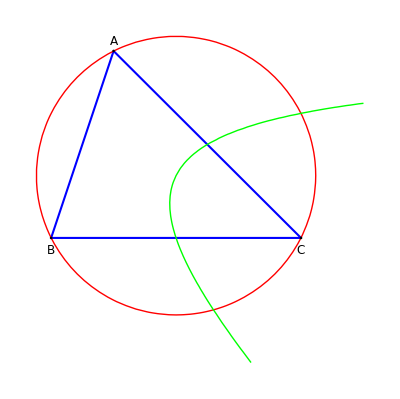

```mathematica
GraficaBaricentricas[{circunscrita,x^2+y^2-z^2},{ContourStyle->{Red,Green}}]
```

## Miscelánea

```mathematica
EsInteriorTriangulo::"usage"=
"EsInterior[ptP,{ptA,ptB,ptC}] devuelve True si el punto P es interior al triángulo ABC";
```

```mathematica
EsInteriorTriangulo[ptP_,{ptA_,ptB_,ptC_}]:=Module[{s,t},
{s,t}={s,t}/.Solve[ptP-ptA==s(ptB-ptA)+t(ptC-ptA)][[1]];
And[
Or[Abs[s]<10^-8,Abs[1-s]<10^-8,And[s>0,s<1]],
Or[Abs[t]<10^-8,Abs[1-t]<10^-8,And[t>0,t<1]]]
]
```

```mathematica
EsInteriorAngulo::"usage"=
"EsInterior[P,{A,B,C}] devuelve True si el punto P es interior al ángulo ABC";
```

```mathematica
EsInteriorAngulo[ptP_,{ptB_,ptA_,ptC_}]:=Module[{s,t},
{s,t}={s,t}/.Solve[ptP-ptA==s(ptB-ptA)+t(ptC-ptA)][[1]];
And[
Or[Abs[s]<10^-8,s>0],
Or[Abs[t]<10^-8,t>0]]
]
```

### Comprobar una desigualdad

```mathematica
EvaluarExpresion::"usage"=
"EvaluarExpresion[expr] evalua una expresión en a, b, c para 10 triángulos elegidos al azar. Se puede usar para investigar si una desigualdad es cierta o no";
```

```mathematica
EvaluarExpresion[expr_]:=Module[{n,x,y,z,a1,b1,c1,lista},
lista={};
For[n=1,n≤ 10,n++,
{x,y,z}=RandomReal[{0,1},3];
{a1,b1,c1}={y+z,z+x,x+y};
lista=Append[lista,{a1,b1,c1, expr/.Thread[{a,b,c}-> {a1,b1,c1}]}]
];
lista //ColumnForm
]
```

Ejemplo :

```mathematica
EvaluarExpresion[a^3-a^2 b-a b^2+b^3-a^2 c-2 a b c-b^2 c-a c^2-b c^2+c^3]
```

{1.51021,1.19354,1.1452,-10.1446}
{1.21384,1.43043,1.59781,-13.7197}
{1.23374,1.09187,1.29462,-8.683}
{0.726182,0.902257,0.204382,-0.550984}
{0.807643,0.908187,1.32485,-4.56938}
{0.842843,1.38472,1.17786,-6.64685}
{1.08261,0.604615,0.938459,-2.94549}
{0.648565,0.174914,0.757419,-0.366774}
{0.859514,0.36985,1.01393,-1.4591}
{0.287433,0.472871,0.759098,-0.413356}

### Transformar una expresión en términos de R, r y p.

```mathematica
Transformar::"usage"=
"Transformar[expr] convierte una expresión (polinómica) simétrica a, b, c en términos de R, r y p. Si la expresión es un cociente, usar TransformarCociente[expr]";
```

```mathematica
Transformar[expr_]:=Factor[SymmetricReduction[
expr,{a,b,c},{2p, p^2+r^2+4R r,4 R r p}][[1]]]
```

```mathematica
TransformarCociente[expr_]:=Factor[
Transformar[Numerator[expr]]/Transformar[Denominator[expr]]]
```

Ejemplo :

```mathematica
Transformar[a^3-a^2 b-a b^2+b^3-a^2 c-2 a b c-b^2 c-a c^2-b c^2+c^3]
```

-8 p r (r+2 R)

Ultimas propuestas de Ércole Suppa

```mathematica
MismoSemipiano::"usage"="MismoSemipiano[X,Y,P,Q}] devuelve True si el punto X,Y appartengono allo stesso semipiano individuato dalla retta PQ";

MismoSemipiano[ptX_,ptY_,ptP_,ptQ_]:=Module[{cX,cY,cP,cQ},{cX,cY,cP,cQ}=Map[PuntoBarCar[#,cA 1.0,cB,cC]&,{ptX,ptY,ptP,ptQ}];
Det[{Append[cX,1],Append[cP,1],Append[cQ,1]}] Det[{Append[cY,1],Append[cP,1],Append[cQ,1]}]>0]
```